```mathematica
Get["DMTestFunctions`"]
Get["DifferenceMapOptimizer`"]
Get["DMData`"]
Get["DMUtils`"]
```

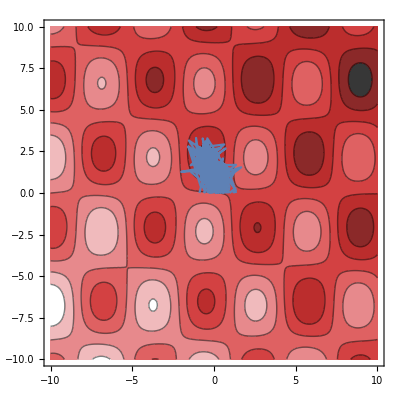
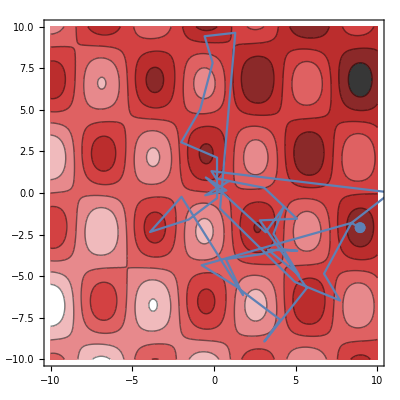
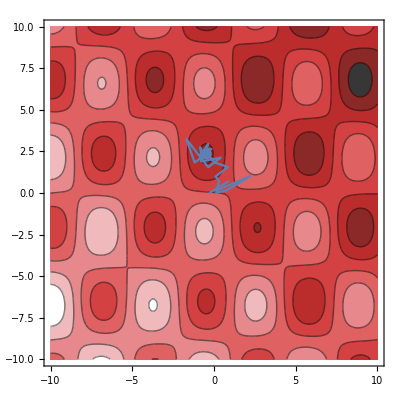
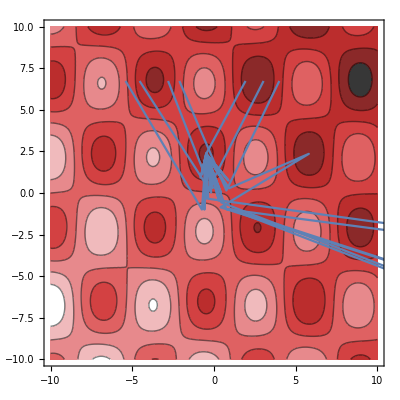
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Automatic | {SimulatedAnnealing,PerturbationScale→5.} | DifferentialEvolution | NelderMead | RandomSearch

```mathematica
builtinMethods = {Automatic, {"SimulatedAnnealing", "PerturbationScale" -> 5.0}, "DifferentialEvolution", "NelderMead", "RandomSearch"};
vars = {x, y};
offset = {100, 100};
range = Sequence[{x, -10, 10}, {y, -10, 10}];
nicePlot[method_] := Module[{fun, solution, minima},
{{fun, solution}, {minima}} =
Reap[
NMinimize[
griewankN[vars - offset],
vars, 
EvaluationMonitor-> Hold[Sow[vars]], 
Method->method, 
MaxIterations->100]
];
Show[
ContourPlot[griewankN[vars - offset], Evaluate[range], PlotPoints -> 45, ColorFunction -> "CherryTones"], ListPlot[minima, Joined->True], 
ListPlot[{Map[# /. solution &, vars]}]
]
];
Grid[{Map[nicePlot, builtinMethods], builtinMethods}]
```

```mathematica
(* Create a plot of the griewank function with the three initial points (x_0, x_0^*, and x_1) overlayed (hard to see.) *)
start = {4, 7};
other = {7, 8};
fun = N[griewankN[start]];
{fun2, solution} = FindMinimum[griewankN[{x, y}], {x, 4}, {y, 7}];
sol = {x, y} /. solution
Show[Plot3D[griewankN[{x, y}], {x, -10, 10}, {y, -10, 10}], ListPointPlot3D[{Join[start, {fun+0.01}],  Join[sol, {fun2+0.02}], Append[other, griewankN[other]]}]]
```

{3.14002,4.43844}

```mathematica
dmSettings = <|
"dim" -> 4,
"niter" -> 100,
"tolerance" -> 1 10^-8,
"runCount" -> 50,
"innerNiter" -> 65,
"secondPointDistance" -> 5.0,
"solversToDo" -> {"dm"},
"maxnfev" -> 20000
|>;
dmResults = makeResults[dmSettings];
```

```mathematica
Export["dmresults.json", dmResults, "JSON"]
```

dmresults.json

```mathematica
as = ToAssociations[dmResults];
```

```mathematica
as[["dm"]][["griewank"]]
```

{<|iterate→{{704.147,438.368,110.373},{699.824,426.448,113.543},{699.856,100.765,246.447},{667.671,89.6691,239.656},94,{12820.3,13638.2,-14941.},{12820.3,13875.2,-15125.6},{12607.2,13724.6,-15168.1}},5,nfev→21345|>,19}
 |  |  |  |

```mathematica
deSettings = <|
"dim" -> 4,
"niter" -> 500,
"tolerance" -> 1 10^-8,
"runCount" -> 50,
"innerNiter" -> 60,
"secondPointDistance" -> 5.0,
"solversToDo" -> {"de"},
"maxnfev" -> 20000
|>;
deResults = makeResults[deSettings];
```

```mathematica
deResultsAs = ToAssociations[deResults];
```

```mathematica
Length[deResultsAs[["de"]][[1]][["iterate"]]]
```

Part::pspec1: Part specification "iterate" is not applicable.

2

```mathematica
stats = ToAssociations[
Map[
Function[s,
s -> Map[
Function[r,
r -> With[{
funvs = Map[#["fun"] &, as[s][r]],
nfevs = Map[#["nfev"] &, as[s][r]]},
{"averageSolution" -> (Plus @@ funvs) / Length[funvs],
"medianSolution" -> Median@funvs,
"minimumSolution" -> Min @@ funvs,
"averageNfevs" -> N[(Plus @@ nfevs) / Length[nfevs]],
"medianNfevs" -> N[Median @ nfevs],
"minimumNfevs" -> N[Min @@ nfevs]
}]
], 
testFunctions[[;;,1]]]], 
builtinSettings["solversToDo"]
]
];
```

```mathematica
stats
```

<|de→<|griewank→<|averageSolution→0.812193,medianSolution→6.72024×10^-12,minimumSolution→1.11022×10^-16,averageNfevs→21324.3,medianNfevs→20644.5,minimumNfevs→20044.|>,rosenbrock→<|averageSolution→0.222281,medianSolution→6.35753×10^-7,minimumSolution→1.78298×10^-9,averageNfevs→29789.5,medianNfevs→25646.5,minimumNfevs→20045.|>,schwefel→<|averageSolution→1675.93,medianSolution→1675.93,minimumSolution→1675.93,averageNfevs→20444.,medianNfevs→20444.,minimumNfevs→20444.|>,schaffer→<|averageSolution→25.6194,medianSolution→26.7068,minimumSolution→9.75453,averageNfevs→20341.1,medianNfevs→20046.,minimumNfevs→20044.|>,ackley→<|averageSolution→5.618,medianSolution→0.,minimumSolution→0.,averageNfevs→20092.,medianNfevs→20044.,minimumNfevs→20044.|>|>,nm→<|griewank→<|averageSolution→47.0564,medianSolution→36.2418,minimumSolution→0.199558,averageNfevs→484.92,medianNfevs→474.5,minimumNfevs→198.|>,rosenbrock→<|averageSolution→0.518205,medianSolution→2.39923×10^-6,minimumSolution→9.03127×10^-13,averageNfevs→899.82,medianNfevs→584.,minimumNfevs→334.|>,schwefel→<|averageSolution→1675.93,medianSolution→1675.93,minimumSolution→1675.93,averageNfevs→2009.,medianNfevs→2009.,minimumNfevs→2009.|>,schaffer→<|averageSolution→25.7189,medianSolution→26.1961,minimumSolution→19.6574,averageNfevs→201.72,medianNfevs→184.,minimumNfevs→116.|>,ackley→<|averageSolution→18.0035,medianSolution→18.8914,minimumSolution→8.71588,averageNfevs→257.62,medianNfevs→253.,minimumNfevs→167.|>|>,rs→<|griewank→<|averageSolution→1.42249,medianSolution→1.07128,minimumSolution→0.0369605,averageNfevs→164.06,medianNfevs→163.,minimumNfevs→163.|>,rosenbrock→<|averageSolution→5.39613×10^-6,medianSolution→3.78454×10^-6,minimumSolution→5.92786×10^-8,averageNfevs→184.54,medianNfevs→180.5,minimumNfevs→173.|>,schwefel→<|averageSolution→1675.93,medianSolution→1675.93,minimumSolution→1675.93,averageNfevs→123.,medianNfevs→123.,minimumNfevs→123.|>,schaffer→<|averageSolution→20.6055,medianSolution→21.9911,minimumSolution→6.7547,averageNfevs→170.48,medianNfevs→170.5,minimumNfevs→163.|>,ackley→<|averageSolution→15.0574,medianSolution→16.615,minimumSolution→2.06218×10^-7,averageNfevs→164.1,medianNfevs→164.,minimumNfevs→163.|>|>|>

```mathematica
Length[Reap[NMinimize[griewankN @ vars, vars, MaxIterations-> 100, Method->{"RandomSearch", "SearchPoints" -> 2000}, EvaluationMonitor->Hold[Sow[1]]]][[2]][[1]]]
```

8003

```mathematica
builtinResults = ToAssociations[
makeResults[
<|
"dim" -> 4,
"niter" -> 1000,
"runCount" -> 3,
"innerNiter" -> 65,
"secondPointDistance" -> 5,
"solversToDo" -> {"sa", "de", "nm", "rs"}
|>
]
];
```

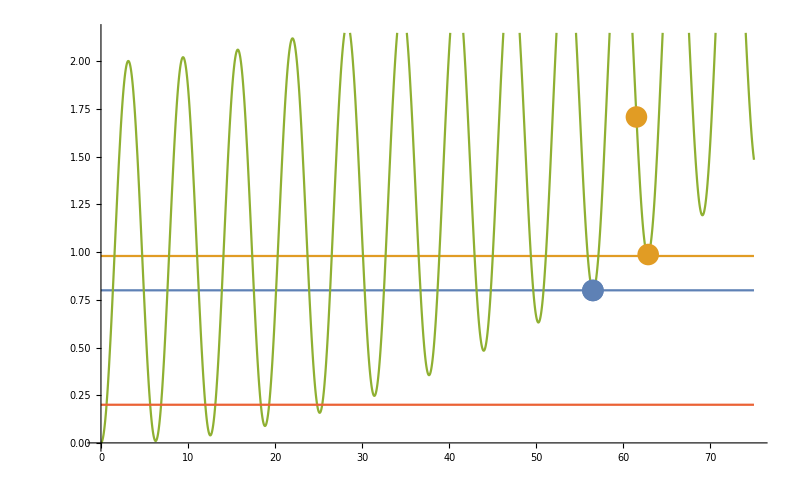

```mathematica
Show[
Plot[{0.8, 0.98, griewankN @ {xi}, 0.2}, {xi, 0, 75}],
ListPlot[{{{56.5, griewankN @ {56.5}}}, {{61.5, griewankN @ {61.5}}, {62.85, griewankN @ {62.85}}}}]
]
```

```mathematica
dim = 4;
niter = 1000;
```